# effect of variance “load” on hybrid fitness

distribution of hybrid traits assumed to be mutlivariate normal, centered at average between two parental optima with variance λ in each direction and no covariance

```mathematica
pxy=PDF[MultinormalDistribution[{(θx1+θx2)/2,(θy1+θy2)/2},{{λ,0},{0,λ}}],{x,y}]
```

ⅇ^(1/2 (-((x+1/2 (-θx1-θx2)) (2 x-θx1-θx2))/(2 λ)-((y+1/2 (-θy1-θy2)) (2 y-θy1-θy2))/(2 λ)))/(2 π √(λ^2))

the fitness functions of each parent environment

```mathematica
wxy1=2 π PDF[MultinormalDistribution[{θx1,θy1},{{1,0},{0,1}}],{x,y}]
wxy2=2 π PDF[MultinormalDistribution[{θx2,θy2},{{1,0},{0,1}}],{x,y}]
```

ⅇ^(1/2 (-(x-θx1)^2-(y-θy1)^2))

ⅇ^(1/2 (-(x-θx2)^2-(y-θy2)^2))

mean fitness of population on a peak with variance λ and its logarithm (chevin’s variance load)

```mathematica
Integrate[wxy1 PDF[MultinormalDistribution[{θx1,θy1},{{λ,0},{0,λ}}],{x,y}]/.θx1->0/.θy1->0,{x,-∞,∞},{y,-∞,∞},Assumptions->λ>0]
varload=-Log[%]
```

1/(1+λ)

-Log[1/(1+λ)]

we will use the above result to convert between variance λ and variance load.

plot mean hybrid fitness relative to mean hybrid fitness in absence of phenotypic variation across different amounts of variance for 3 amounts of divergent selection

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

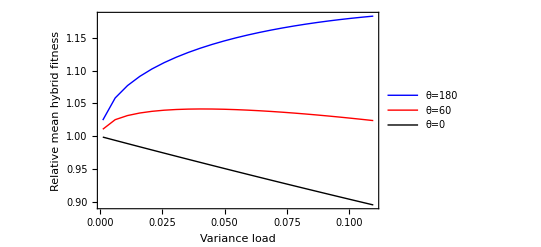

```mathematica
colors={Directive[Thick,Blue],Directive[Thick,Red],Directive[Thick,Black]};
legend={"θ=180","θ=60","θ=0"};
θx1=1;
θy1=0;
θx2=Cos[θ*π/180];
θy2=Sin[θ*π/180];
θs={180,60,0};nθ=Length[θs];

novar=(wxy1/.x->(θx1+θx2)/2/.y->(θy1+θy2)/2);

Table[{varload,NIntegrate[Max[wxy1,wxy2]pxy/.θ->θs[[i]],{x,-∞,∞},{y,-∞,∞}]/novar/.θ->θs[[i]]},{i,Length[θs]},{λ,10^-3,0.12,0.005}];
ListPlot[%,Joined->True,PlotRange->All,Frame->{True,True,False,False},FrameLabel->{Style["Variance load",16],Style["Relative mean hybrid fitness",16]},PlotStyle->colors,PlotLegends->Placed[LineLegend[colors,legend],Right],FrameStyle->Directive[FontSize->16]]
Export[NotebookDirectory[]<>"loadfit.pdf",%];

Clear[θx1,θx2,θy1,θy2,θs,θ]
```

save data for plotting in R

```mathematica
colors={Directive[Thick,Blue],Directive[Thick,Red],Directive[Thick,Black]};
legend={"θ=180","θ=60","θ=0"};
θx1=1;
θy1=0;
θx2=Cos[θ*π/180];
θy2=Sin[θ*π/180];
θs={180,60,0};nθ=Length[θs];

novar=(wxy1/.x->(θx1+θx2)/2/.y->(θy1+θy2)/2);

Table[{θs[[i]],varload,NIntegrate[Max[wxy1,wxy2]pxy/.θ->θs[[i]],{x,-∞,∞},{y,-∞,∞}]/novar/.θ->θs[[i]]},{i,Length[θs]},{λ,10^-3,0.12,0.005}];
Flatten[%,1];
Export[NotebookDirectory[]<>"loadfit.csv",%,"CSV"];

Clear[θx1,θx2,θy1,θy2,θs,θ]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.